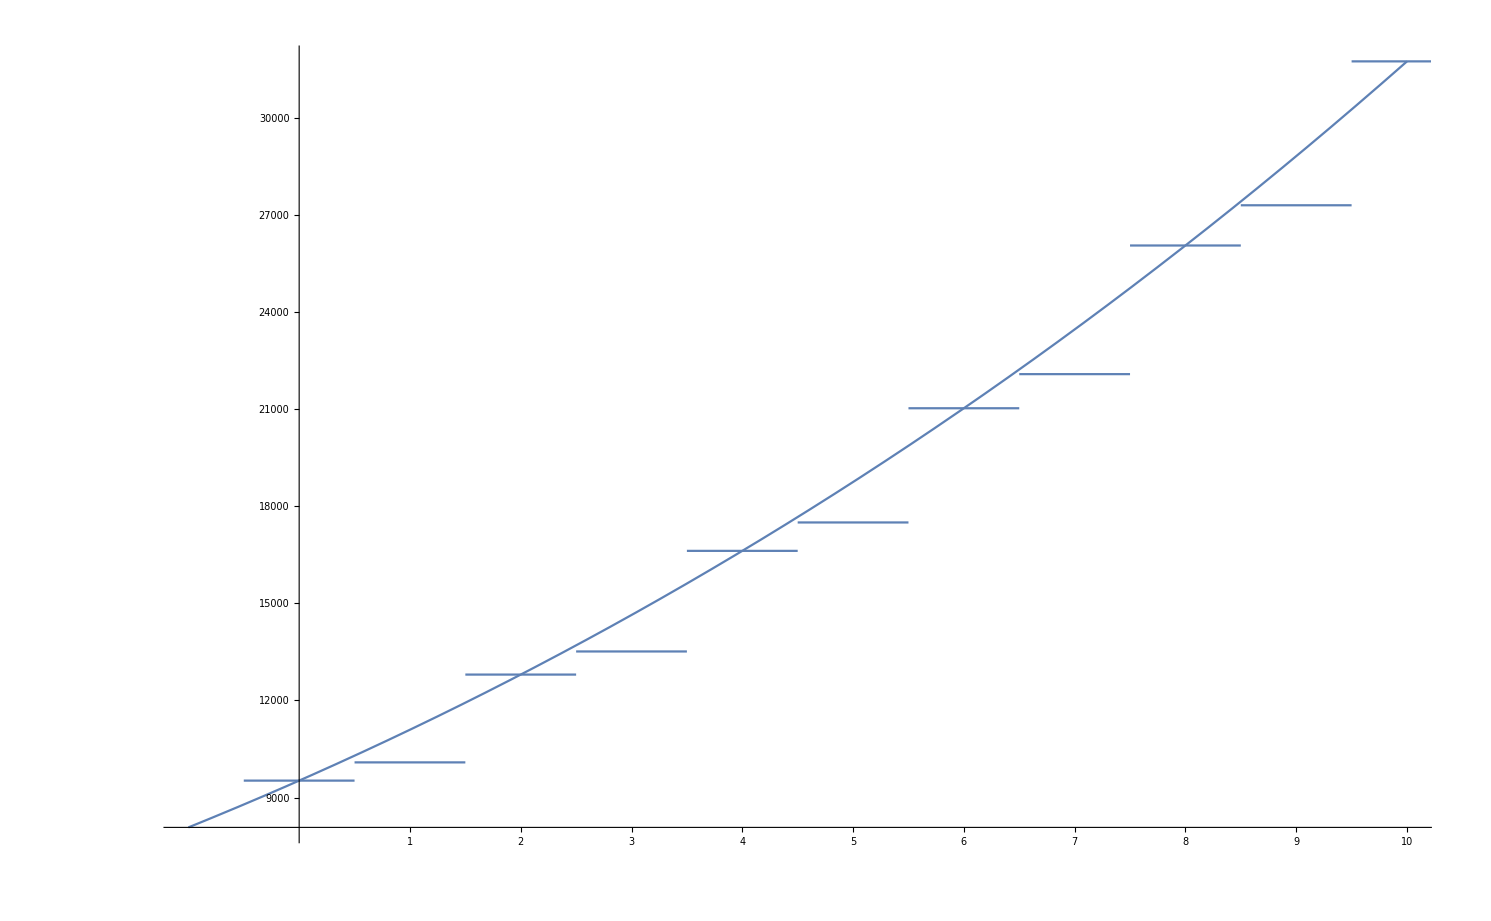

```mathematica
Clear[c,d]
d=DiscretePlot[{y=634.95*(0.025x+1)*(0.1x+3)*(5+Floor[0.5x])},{x,0,10},ExtentSize->Full,Filling->None];
c=Plot[{y=634.95*(0.025x+1)*(0.1x+3)*(5+0.5x)},{x,-1,10},PlotRange->Automatic,Ticks->{Range[10],Automatic}];
Show[c,d]
```